```mathematica
qi[k_]:=(q^k-q^-k)/(q-q^-1)
```

```mathematica
ν[m_][i_][T[i_,j_]]:=(-1)^j qi[m]^-1(
If[j>0,(-1)^(m-i)qi[i+j]T[i+1,j-1],0]+
If[i+j>m/2,(-1)^(m/2)qi[2i+j-m/2]T[i+1,j-2],0]+
If[i+j<m/2,(-1)^(m/2)qi[j+m/2]T[i+1,j],0]
)
```

```mathematica
ν[m_][i_][a_ t_T]:=a ν[m][i][t]
ν[m_][i_][X_Plus]:=ν[m][i]/@X
```

```mathematica
μ[m_][i_][T[i_,j_]]:=(-1)^i qi[m]^-1(qi[m-i]T[i,j+1]+(-1)^m qi[i]T[i,j-1])
```

```mathematica
μ[m_][i_][a_ t_T]:=a μ[m][i][t]
μ[m_][i_][X_Plus]:=μ[m][i]/@X
μ[m_][i_][X_Times]:=μ[m][i][Expand[X]]
```

```mathematica
With[{m=10,i=2,r=2},
With[{v=Sum[ζ[m-2i]^(j r)T[i,j],{j,0,m-2i-1}]},
Collect[
μ[m][i][v]-((-1)^i qi[m]^-1(qi[m-i] ζ[m-2i]^-r+(-1)^m qi[i] ζ[m-2i]^r))v/.{T[i,m-2i]:>T[i,0],T[i,-1]:>T[i,m-2i-1],ζ[k_]:>Exp[2π ⅈ/k]},
_T,Together]
]
]
```

0

```mathematica
(* The minus sign in the exponent of the root here is correct; confusion reigns when switching from matrices to linear transformations... *)
resμ[m_][i_,z_][T[i_,j_]]:=Sum[
1/(m-2i)(Sum[ζ[m-2i]^(-ℓ(j-jp))((-1)^i qi[m-i]/qi[m] ζ[m-2i]^-ℓ+(-1)^(m-i)qi[i]/qi[m] ζ[m-2i]^ℓ-z)^-1,{ℓ,0,m-2i-1}])T[i,jp]
,{jp,0,m-2i-1}]
```

```mathematica
resμ[m_][i_,z_][a_ t_T]:=a resμ[m][i,z][t]
resμ[m_][i_,z_][X_Plus]:=resμ[m][i,z]/@X
resμ[m_][i_,z_][X_Times]:=resμ[m][i,z][Expand[X]]
```

```mathematica
With[{m=10,i=0,j=0},Collect[resμ[m][i,z][μ[m][i][T[i,j]]-z T[i,j]]/.ζ[k_]:>Exp[2π ⅈ/k],_T,FullSimplify]]
```

T[0,0]

```mathematica
With[{m=10,i=1,j=2},Collect[resμ[m][i,z][μ[m][i][T[i,j]]-z T[i,j]]/.ζ[k_]:>Exp[2π ⅈ/k],_T,Together]]
```

T[1,2]

```mathematica
Coefficient[%,T[1,0]]
```

-((ⅈ (4 ⅈ q^6 z^2+24 ⅈ q^8 z^2+84 ⅈ q^10 z^2+224 ⅈ q^12 z^2+504 ⅈ q^14 z^2+1008 ⅈ q^16 z^2+1848 ⅈ q^18 z^2+3168 ⅈ q^20 z^2+5148 ⅈ q^22 z^2+7984 ⅈ q^24 z^2+11868 ⅈ q^26 z^2+16968 ⅈ q^28 z^2+23408 ⅈ q^30 z^2+31248 ⅈ q^32 z^2+40464 ⅈ q^34 z^2+50928 ⅈ q^36 z^2+62400 ⅈ q^38 z^2+74472 ⅈ q^40 z^2+86644 ⅈ q^42 z^2+98352 ⅈ q^44 z^2+109008 ⅈ q^46 z^2+118040 ⅈ q^48 z^2+124932 ⅈ q^50 z^2+129264 ⅈ q^52 z^2+130752 ⅈ q^54 z^2+129264 ⅈ q^56 z^2+124932 ⅈ q^58 z^2+118040 ⅈ q^60 z^2+109008 ⅈ q^62 z^2+98352 ⅈ q^64 z^2+86644 ⅈ q^66 z^2+74472 ⅈ q^68 z^2+62400 ⅈ q^70 z^2+50928 ⅈ q^72 z^2+40464 ⅈ q^74 z^2+31248 ⅈ q^76 z^2+23408 ⅈ q^78 z^2+16968 ⅈ q^80 z^2+11868 ⅈ q^82 z^2+7984 ⅈ q^84 z^2+5148 ⅈ q^86 z^2+3168 ⅈ q^88 z^2+1848 ⅈ q^90 z^2+1008 ⅈ q^92 z^2+504 ⅈ q^94 z^2+224 ⅈ q^96 z^2+84 ⅈ q^98 z^2+24 ⅈ q^100 z^2+4 ⅈ q^102 z^2-16 ⅈ q^28 z^4-48 ⅈ q^30 z^4-96 ⅈ q^32 z^4-160 ⅈ q^34 z^4-240 ⅈ q^36 z^4-336 ⅈ q^38 z^4-448 ⅈ q^40 z^4-576 ⅈ q^42 z^4-720 ⅈ q^44 z^4-864 ⅈ q^46 z^4-976 ⅈ q^48 z^4-1056 ⅈ q^50 z^4-1104 ⅈ q^52 z^4-1120 ⅈ q^54 z^4-1104 ⅈ q^56 z^4-1056 ⅈ q^58 z^4-976 ⅈ q^60 z^4-864 ⅈ q^62 z^4-720 ⅈ q^64 z^4-576 ⅈ q^66 z^4-448 ⅈ q^68 z^4-336 ⅈ q^70 z^4-240 ⅈ q^72 z^4-160 ⅈ q^74 z^4-96 ⅈ q^76 z^4-48 ⅈ q^78 z^4-16 ⅈ q^80 z^4+4 ⅈ q^18 z^6+16 ⅈ q^20 z^6+40 ⅈ q^22 z^6+80 ⅈ q^24 z^6+140 ⅈ q^26 z^6+224 ⅈ q^28 z^6+336 ⅈ q^30 z^6+480 ⅈ q^32 z^6+660 ⅈ q^34 z^6+880 ⅈ q^36 z^6+1128 ⅈ q^38 z^6+1392 ⅈ q^40 z^6+1660 ⅈ q^42 z^6+1920 ⅈ q^44 z^6+2160 ⅈ q^46 z^6+2368 ⅈ q^48 z^6+2532 ⅈ q^50 z^6+2640 ⅈ q^52 z^6+2680 ⅈ q^54 z^6+2640 ⅈ q^56 z^6+2532 ⅈ q^58 z^6+2368 ⅈ q^60 z^6+2160 ⅈ q^62 z^6+1920 ⅈ q^64 z^6+1660 ⅈ q^66 z^6+1392 ⅈ q^68 z^6+1128 ⅈ q^70 z^6+880 ⅈ q^72 z^6+660 ⅈ q^74 z^6+480 ⅈ q^76 z^6+336 ⅈ q^78 z^6+224 ⅈ q^80 z^6+140 ⅈ q^82 z^6+80 ⅈ q^84 z^6+40 ⅈ q^86 z^6+16 ⅈ q^88 z^6+4 ⅈ q^90 z^6))/(2 (-ⅈ q-ⅈ q^3-ⅈ q^5-ⅈ q^7+z+q^2 z+q^4 z+q^6 z+q^8 z) (ⅈ q+ⅈ q^3+ⅈ q^5+ⅈ q^7+z+q^2 z+q^4 z+q^6 z+q^8 z) (-q-q^9+z+q^10 z) (q+q^9+z+q^10 z) (ⅈ q+ⅈ q^3+ⅈ q^5+ⅈ q^7+(1+ⅈ) q^9+ⅈ q^11+ⅈ q^13+ⅈ q^15+ⅈ q^17+(-1)^(1/4) z+(-1)^(1/4) q^2 z+(-1)^(1/4) q^4 z+(-1)^(1/4) q^6 z+(-1)^(1/4) q^8 z+(-1)^(1/4) q^10 z+(-1)^(1/4) q^12 z+(-1)^(1/4) q^14 z+(-1)^(1/4) q^16 z+(-1)^(1/4) q^18 z) (q+q^3+q^5+q^7+(1+ⅈ) q^9+q^11+q^13+q^15+q^17+(-1)^(1/4) z+(-1)^(1/4) q^2 z+(-1)^(1/4) q^4 z+(-1)^(1/4) q^6 z+(-1)^(1/4) q^8 z+(-1)^(1/4) q^10 z+(-1)^(1/4) q^12 z+(-1)^(1/4) q^14 z+(-1)^(1/4) q^16 z+(-1)^(1/4) q^18 z) (-ⅈ q-ⅈ q^3-ⅈ q^5-ⅈ q^7+(1-ⅈ) q^9-ⅈ q^11-ⅈ q^13-ⅈ q^15-ⅈ q^17+(-1)^(3/4) z+(-1)^(3/4) q^2 z+(-1)^(3/4) q^4 z+(-1)^(3/4) q^6 z+(-1)^(3/4) q^8 z+(-1)^(3/4) q^10 z+(-1)^(3/4) q^12 z+(-1)^(3/4) q^14 z+(-1)^(3/4) q^16 z+(-1)^(3/4) q^18 z) (q+q^3+q^5+q^7+(1-ⅈ) q^9+q^11+q^13+q^15+q^17+(-1)^(3/4) z+(-1)^(3/4) q^2 z+(-1)^(3/4) q^4 z+(-1)^(3/4) q^6 z+(-1)^(3/4) q^8 z+(-1)^(3/4) q^10 z+(-1)^(3/4) q^12 z+(-1)^(3/4) q^14 z+(-1)^(3/4) q^16 z+(-1)^(3/4) q^18 z)))

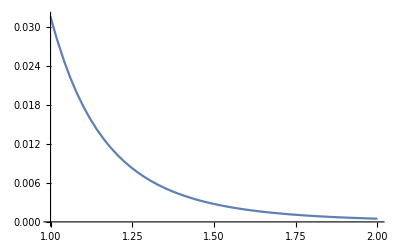

```mathematica
Plot[%31/.q->2,{z,1,2}]
```

```mathematica
FullSimplify[%]
```

$Aborted

```mathematica
Clear[X]
X[m_,ω_][0]:=Sum[ω^-j T[0,j],{j,0,m-1}]
X[m_,ω_][i_]:=X[m,ω][i]=Collect[-resμ[m][i,ω][ν[m][i-1][X[m,ω][i-1]]],_T,Together]
```

```mathematica
Clear[ζ]
```

```mathematica
ζ/:ζ[n_]^m_/;m≥n:=ζ[n]^Mod[m,n]
```

```mathematica
ζ/:ζ[8]^(n_?EvenQ):=ⅈ^(n/2)
ζ/:ζ[8]^(n_?OddQ):=ⅈ^((n-1)/2)ζ[8]
```

```mathematica
ζ/:ζ[6]^(n_/;n≥3):=ζ[6]^Mod[n,3](-1)^Floor[n/3]
```

```mathematica
γ[j_]/;j>1:=γ[Mod[j,2]]
```

```mathematica
Clear[a]
a[m_][σ_,ω_]:=a[m][σ,ω]=Collect[X[m,ω][1]/.T[1,j_]:>σ^j γ[j+1],_γ,Together]
```

```mathematica
Clear[b]
b[n_][σ_,ω_]:=b[n][σ,ω]=∑_(j=0)^n (ω^-j+ω^(-j+n+1))((-1)^j(σ^j qi[2n+2-j]+σ^(j-2)qi[j])γ[j]+(-1)^(n+j+1)(σ^(j+1)qi[n+1-j]+σ^(j-1)qi[n+1+j])γ[j+1])
```

```mathematica
Clear[Z]
Z[n_,σ_,ω_]:=Z[n,σ,ω]=a[2n+2][σ,ω](q^(2n+2)+q^(-2n-2)-σ^2-σ^-2)+b[n][σ,ω]
```

Ok, we have everything set up.  Recall this abstractly only works for unshaded planar algebras with our current setup, so lets check the data for 2221.  Here n=3, and σ=1, e^(4 πi/3).  Lets check for all Tenth roots of unity ω:

```mathematica
Simplify[Together[Z[3,1,1]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

0

```mathematica
Simplify[Together[Z[3,1,Exp[2π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,1,Exp[4π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

0

```mathematica
Simplify[Together[Z[3,1,Exp[6π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

$Aborted

```mathematica
Simplify[Together[Z[3,1,Exp[8π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,1,Exp[10π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,1,Exp[12π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,1,Exp[14π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,Exp[4π ⅈ/3],1]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,Exp[4π ⅈ/3],Exp[2π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,Exp[4π ⅈ/3],Exp[4π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,Exp[4π ⅈ/3],Exp[6π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,Exp[4π ⅈ/3],Exp[8π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,Exp[4π ⅈ/3],Exp[10π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,Exp[4π ⅈ/3],Exp[12π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

```mathematica
Simplify[Together[Z[3,Exp[4π ⅈ/3],Exp[14π ⅈ/8]]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

Now lets see what happens when we plug in a ``wrong” value for σ.... (spoiler alert, it goes haywire!)

```mathematica
w=Simplify[Together[Z[3,Exp[2π ⅈ/3],1]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]]
```

0

```mathematica
(* What about sigma just of the wrong order? *)
w=Simplify[Together[Z[3,Exp[10π ⅈ/8],1]/._γ->1/.ζ[6]:>Exp[2π ⅈ/6]]];
```

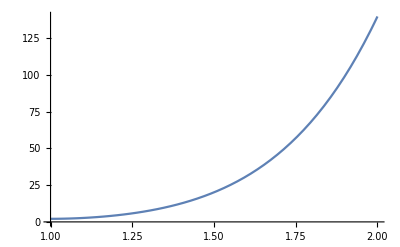

```mathematica
Plot[Abs[w],{q,1,2}]
```

This implies that our equation is non-trivial?  It looks like it could provide serious obstructions for the eigenvalues of generators?  Just to be sure we are not just getting lucky, lets check 4442 (also unshaded).  n=5, and σ=e^(2πi 8/10), which takes quite a long time...

```mathematica
v=Simplify[Together[Z[5,Exp[4π ⅈ/10],1]/._γ->1/.ζ[10]:>Exp[2π ⅈ/10]]]
```

-((8 (-1)^(1/5) (1-(-1)^(1/5)+(-1)^(2/5)-(-1)^(3/5)+(-1)^(4/5)) (-1+q)^10 (1+q)^8 (1+q^2+q^4+q^6+q^8+q^10)^10 (1+q^2+q^4+q^6+q^8+q^10+q^12+q^14+q^16+q^18+q^20)^4)/(5 q^11 (1+(-1)^(3/5) q+q^2+(-1)^(3/5) q^3+q^4+(-1)^(3/5) q^5+q^6+(-1)^(3/5) q^7+q^8+(-1)^(3/5) q^9+q^10+(-1)^(2/5) (-1+(-1)^(1/5)) q^11+q^12+(-1)^(3/5) q^13+q^14+(-1)^(3/5) q^15+q^16+(-1)^(3/5) q^17+q^18+(-1)^(3/5) q^19+q^20+(-1)^(3/5) q^21+q^22) (1+(-1)^(4/5) q+q^2+(-1)^(4/5) q^3+q^4+(-1)^(4/5) q^5+q^6+(-1)^(4/5) q^7+q^8+(-1)^(4/5) q^9+q^10+(-1)^(1/5) (-1+(-1)^(3/5)) q^11+q^12+(-1)^(4/5) q^13+q^14+(-1)^(4/5) q^15+q^16+(-1)^(4/5) q^17+q^18+(-1)^(4/5) q^19+q^20+(-1)^(4/5) q^21+q^22) ((-1)^(1/5)+q+(-1)^(1/5) q^2+q^3+(-1)^(1/5) q^4+q^5+(-1)^(1/5) q^6+q^7+(-1)^(1/5) q^8+q^9+(-1)^(1/5) q^10+(1+(-1)^(2/5)) q^11+(-1)^(1/5) q^12+q^13+(-1)^(1/5) q^14+q^15+(-1)^(1/5) q^16+q^17+(-1)^(1/5) q^18+q^19+(-1)^(1/5) q^20+q^21+(-1)^(1/5) q^22) ((-1)^(1/5)-(-1)^(2/5) q+(-1)^(1/5) q^2-(-1)^(2/5) q^3+(-1)^(1/5) q^4-(-1)^(2/5) q^5+(-1)^(1/5) q^6-(-1)^(2/5) q^7+(-1)^(1/5) q^8-(-1)^(2/5) q^9+(-1)^(1/5) q^10-(1+(-1)^(2/5)) q^11+(-1)^(1/5) q^12-(-1)^(2/5) q^13+(-1)^(1/5) q^14-(-1)^(2/5) q^15+(-1)^(1/5) q^16-(-1)^(2/5) q^17+(-1)^(1/5) q^18-(-1)^(2/5) q^19+(-1)^(1/5) q^20-(-1)^(2/5) q^21+(-1)^(1/5) q^22) ((-1)^(1/5)+(-1)^(2/5) q+(-1)^(1/5) q^2+(-1)^(2/5) q^3+(-1)^(1/5) q^4+(-1)^(2/5) q^5+(-1)^(1/5) q^6+(-1)^(2/5) q^7+(-1)^(1/5) q^8+(-1)^(2/5) q^9+(-1)^(1/5) q^10+(1+(-1)^(2/5)) q^11+(-1)^(1/5) q^12+(-1)^(2/5) q^13+(-1)^(1/5) q^14+(-1)^(2/5) q^15+(-1)^(1/5) q^16+(-1)^(2/5) q^17+(-1)^(1/5) q^18+(-1)^(2/5) q^19+(-1)^(1/5) q^20+(-1)^(2/5) q^21+(-1)^(1/5) q^22) ((-1)^(2/5)+q+(-1)^(2/5) q^2+q^3+(-1)^(2/5) q^4+q^5+(-1)^(2/5) q^6+q^7+(-1)^(2/5) q^8+q^9+(-1)^(2/5) q^10+(1+(-1)^(4/5)) q^11+(-1)^(2/5) q^12+q^13+(-1)^(2/5) q^14+q^15+(-1)^(2/5) q^16+q^17+(-1)^(2/5) q^18+q^19+(-1)^(2/5) q^20+q^21+(-1)^(2/5) q^22) ((-1)^(2/5)-(-1)^(4/5) q+(-1)^(2/5) q^2-(-1)^(4/5) q^3+(-1)^(2/5) q^4-(-1)^(4/5) q^5+(-1)^(2/5) q^6-(-1)^(4/5) q^7+(-1)^(2/5) q^8-(-1)^(4/5) q^9+(-1)^(2/5) q^10-(1+(-1)^(4/5)) q^11+(-1)^(2/5) q^12-(-1)^(4/5) q^13+(-1)^(2/5) q^14-(-1)^(4/5) q^15+(-1)^(2/5) q^16-(-1)^(4/5) q^17+(-1)^(2/5) q^18-(-1)^(4/5) q^19+(-1)^(2/5) q^20-(-1)^(4/5) q^21+(-1)^(2/5) q^22) ((-1)^(2/5)+(-1)^(4/5) q+(-1)^(2/5) q^2+(-1)^(4/5) q^3+(-1)^(2/5) q^4+(-1)^(4/5) q^5+(-1)^(2/5) q^6+(-1)^(4/5) q^7+(-1)^(2/5) q^8+(-1)^(4/5) q^9+(-1)^(2/5) q^10+(1+(-1)^(4/5)) q^11+(-1)^(2/5) q^12+(-1)^(4/5) q^13+(-1)^(2/5) q^14+(-1)^(4/5) q^15+(-1)^(2/5) q^16+(-1)^(4/5) q^17+(-1)^(2/5) q^18+(-1)^(4/5) q^19+(-1)^(2/5) q^20+(-1)^(4/5) q^21+(-1)^(2/5) q^22)))

Ok, lets find the value of q in 4442 and plug it in to the above expression....

```mathematica
Clear[qFromd]
qFromd[d_]:=qFromd[d]=RootReduce[Max[q/.Solve[q+q^(-1)==Sqrt[3+Sqrt[5]], q, Reals]]]
```

```mathematica
v/.q->qFromd[√(3+√5)]//RootReduce
```

0

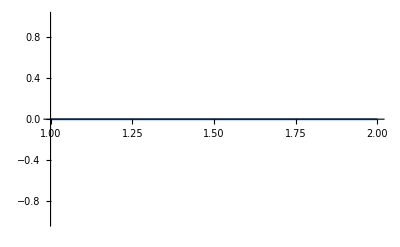

```mathematica
Plot[Abs[v],{q,1,2}]
```